# Nakagami channel detection probability (optimum m n)

This notebook demonstrates the convergence of the Nakagami signal to noise ratio PDF to a normal distribution with increasing m n.  The absolute and relative errors are then plotted against increasing m n so that a suitable switching point between the large m n and integer m n approximations can be found.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

27/06/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
nRange={1,2,3,4,5,10,20};
mRange={0.5,1,1.5,2};
samplesRange={1000,10000,50000};
snrdbRange=Range[0,-21,-1];
snrRange=10^(snrdbRange/10);
pfRange={49/100,30/100,20/100,10/100,5/100,1/100,5/1000,1/1000,5/10000,1/10000,5/100000,1/100000};
```

Here, we select n and m so that m n ∈ I:

```mathematica
{nRange,mRange,mnRange}=Select[Flatten[Table[{nRange⟦i⟧,mRange⟦j⟧,nRange⟦i⟧ mRange⟦j⟧},{i,Length[nRange]},{j,Length[mRange]}],1],Ceiling[##[[3]]]==##[[3]]&]//Transpose;
```

## Calculations

Calculate the probability of detection, for each set of parameter values defined previously, using the exact and approximate methods:

```mathematica
exact=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Exact"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ExactAnnamalai",DatabaseLookup->True],{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

```mathematica
approx=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Approximate"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ApproximateAsymptotic"],{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

$Aborted

Calculate various error metrics:

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

Calculate the square error between the PDF of the Nakagami-faded signal to noise ratio and its approximant:

```mathematica
squareError=(exact-approx)^2;
```

```mathematica
squareErrorPDF=Quiet[ParallelTable[
Table[(NakagamiPDF[10^(snrdb/10),mRange[[mn]],10^(x/10),nRange[[mn]]]-NakagamiPDF[10^(snrdb/10),mRange[[mn]],10^(x/10),nRange[[mn]],Method->"Approximate"])^2//N,{x,Range[nRange[[mn]] 10^(snrdb/10)-6 √((nRange[[mn]] (10^(snrdb/10))^2)/mRange[[mn]])//N,nRange[[mn]] 10^(snrdb/10)+6 √((nRange[[mn]] (10^(snrdb/10))^2)/mRange[[mn]])//N,1/100 √((nRange[[mn]] (10^(snrdb/10))^2)/mRange[[mn]])//N]}]
,
{snrdb,-21,0},
{mn,Length[mnRange]}
]];
```

## Results

### Plot of relative error against m n

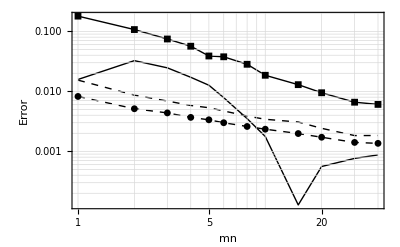

```mathematica
MNPlot[relError,squareErrorPDF,{"|OverBar[ϵ_r]|","σ_ϵ_r","OverBar[ϵ_s]","σ_ϵ_s"}]
```

### Plot of absolute error against m n

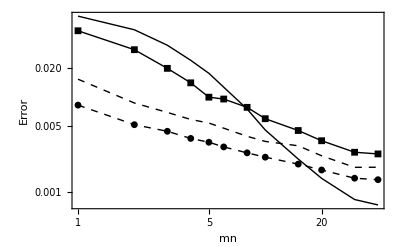

```mathematica
MNPlot[absError,squareErrorPDF,{"|OverBar[ϵ_r]|","σ_ϵ_r","OverBar[ϵ_s]","σ_ϵ_s"}]
```